```mathematica
Table[Indexed[a,i],{i,1,10}].Table[Indexed[b,i],{i,1,10}]
```

a1 b1+a2 b2+a3 b3+a4 b4+a5 b5+a6 b6+a7 b7+a8 b8+a9 b9+a10 b10

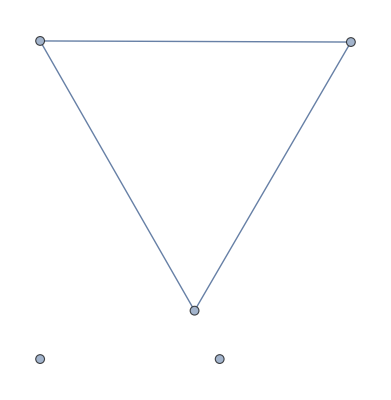

```mathematica
Graph[{1,2,3,4,5},{1<->2,1<->3,3<->2}]
```

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,3<->2}],allGraphs5[#,"graph"]]&]
```

{26487,21951,20439,8757,7293,2917,333,273,109,13}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,3<->2}],allGraphs5[#,"graph"]]&]}
]
```

{-Graphics-26487,-Graphics-21951,-Graphics-20439,-Graphics-8757,-Graphics-7293,-Graphics-2917,-Graphics-333,-Graphics-273,-Graphics-109,-Graphics-13}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2}],allGraphs5[#,"graph"]]&]}
]
```

{-Graphics-19683,-Graphics-6561,-Graphics-2187,-Graphics-729,-Graphics-243,-Graphics-81,-Graphics-27,-Graphics-9,-Graphics-3,-Graphics-1}

```mathematica
s123=With[
{searck=26487},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{487,517,516,577,607,606,576,486,1216,1246,1245,1306,1336,1335,1305,1215,2674,2704,2703,2764,2794,2793,2763,2673,3403,3433,3432,3493,3523,3522,3492,3402,26731,26761,26760,26821,26851,26850,26820,26730,27460,27490,27489,27550,27580,27579,27549,27459,28918,28948,28947,29008,29038,29037,29007,28917,29647,29677,29676,29737,29767,29766,29736,29646,39367,39370,39369,39376,39379,39378,39375,40123,40126,40125,40132,40135,40134,40131,40122,41635,41638,41637,41644,41647,41646,41643,42391,42394,42393,42400,42403,42402,42399,42390,41634,46171,46174,46173,46180,46183,46182,46179,46927,46930,46929,46936,46939,46938,46935,46926,48439,48442,48441,48448,48451,48450,48447,49195,49198,49197,49204,49207,49206,49203,49194,48438,46170,39366,13123,13150,13149,13204,13231,13230,13203,13855,13882,13881,13936,13963,13962,13935,13854,15319,15346,15345,15400,15427,15426,15399,16051,16078,16077,16132,16159,16158,16131,16050,15318,13122,33049,33076,33075,33130,33157,33156,33129,33781,33808,33807,33862,33889,33888,33861,33780,35245,35272,35271,35326,35353,35352,35325,35977,36004,36003,36058,36085,36084,36057,35976,35244,33048,488,608,3404,3524,26732,26852,29648,29768,39368,39380,42392,42404,46172,46184,49196,49208,39388,39384,40144,40140,48460,48456,49216,49212,39372,39382,41640,41650,46932,46942,49200,49210,13124,13232,16052,16160,33050,33158,35978,36086,13312,13284,14044,14016,35434,35406,36166,36138,13176,13258,15372,15454,33834,33916,36030,36112,4890,4860,5620,5590,31224,31194,31954,31924,2034,1944,4222,4132,28308,28218,30496,30406,697,666,1426,1395,29128,29097,29857,29826,546,637,2733,2824,27519,27610,29706,29797,52975,53734,53733,55252,56011,56010,55251,52974,43905,44662,44659,43902,50718,51475,51472,50715,40887,40878,43156,43147,47694,47685,49963,49954,17541,18274,18247,17514,37548,38281,38254,37521,14667,14586,16864,16783,34620,34539,36817,36736,39392,49220,52976,56012,43908,51478,40896,49972,13340,36194,17568,38308,14748,36898,4920,31984,6320,32684,2124,30586,728,29888,58288,57528,54492,56770,45416,52232,18980,39014,59048}

```mathematica
s12=With[
{searck=19683},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{39367,39370,39369,39376,39379,39378,39375,40123,40126,40125,40132,40135,40134,40131,40122,41635,41638,41637,41644,41647,41646,41643,42391,42394,42393,42400,42403,42402,42399,42390,41634,46171,46174,46173,46180,46183,46182,46179,46927,46930,46929,46936,46939,46938,46935,46926,48439,48442,48441,48448,48451,48450,48447,49195,49198,49197,49204,49207,49206,49203,49194,48438,46170,39366,39368,39380,42392,42404,46172,46184,49196,49208,39388,39384,40144,40140,48460,48456,49216,49212,39372,39382,41640,41650,46932,46942,49200,49210,52975,53734,53733,55252,56011,56010,55251,52974,43905,44662,44659,43902,50718,51475,51472,50715,40887,40878,43156,43147,47694,47685,49963,49954,39392,49220,52976,56012,43908,51478,40896,49972,58288,57528,54492,56770,45416,52232,59048}

```mathematica
s23=With[
{searck=243},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{487,517,516,577,607,606,576,486,1216,1246,1245,1306,1336,1335,1305,1215,2674,2704,2703,2764,2794,2793,2763,2673,3403,3433,3432,3493,3523,3522,3492,3402,26731,26761,26760,26821,26851,26850,26820,26730,27460,27490,27489,27550,27580,27579,27549,27459,28918,28948,28947,29008,29038,29037,29007,28917,29647,29677,29676,29737,29767,29766,29736,29646,488,608,3404,3524,26732,26852,29648,29768,4890,4860,5620,5590,31224,31194,31954,31924,2034,1944,4222,4132,28308,28218,30496,30406,697,666,1426,1395,29128,29097,29857,29826,546,637,2733,2824,27519,27610,29706,29797,52975,53734,53733,55252,56011,56010,55251,52974,52976,56012,4920,31984,6320,32684,2124,30586,728,29888,58288,57528,54492,56770,59048}

```mathematica
s13=With[
{searck=6561},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{13123,13150,13149,13204,13231,13230,13203,13855,13882,13881,13936,13963,13962,13935,13854,15319,15346,15345,15400,15427,15426,15399,16051,16078,16077,16132,16159,16158,16131,16050,15318,13122,33049,33076,33075,33130,33157,33156,33129,33781,33808,33807,33862,33889,33888,33861,33780,35245,35272,35271,35326,35353,35352,35325,35977,36004,36003,36058,36085,36084,36057,35976,35244,33048,13124,13232,16052,16160,33050,33158,35978,36086,13312,13284,14044,14016,35434,35406,36166,36138,13176,13258,15372,15454,33834,33916,36030,36112,52975,53734,53733,55252,56011,56010,55251,52974,17541,18274,18247,17514,37548,38281,38254,37521,14667,14586,16864,16783,34620,34539,36817,36736,52976,56012,13340,36194,17568,38308,14748,36898,58288,57528,54492,56770,18980,39014,59048}

```mathematica
{Length[s123],Length[s12],Length[s13],Length[s23]}
```

{351,127,127,127}

```mathematica
{Length[s123],Length[DeleteDuplicates[Join[s12,s13,s23]]]}
```

{351,351}

## Now the same but only orthogonal base vectors

```mathematica
s123=With[
{searck=26487},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29767,49207,36085,29768,49208,49216,49210,36086,36166,36112,31954,30496,29857,29797,56011,51475,49963,38281,36817,49220,56012,51478,49972,36194,38308,36898,31984,32684,30586,29888,58288,56770,52232,39014,59048}

```mathematica
Length[s123]
```

35

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s123}
]
```

{-Graphics-29767,-Graphics-49207,-Graphics-36085,-Graphics-29768,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-31954,-Graphics-30496,-Graphics-29857,-Graphics-29797,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-38281,-Graphics-36817,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-31984,-Graphics-32684,-Graphics-30586,-Graphics-29888,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-39014,-Graphics-59048}

```mathematica
s12=With[
{searck=19683},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{49207,49208,49216,49210,56011,51475,49963,49220,56012,51478,49972,58288,56770,52232,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s12}
]
```

{-Graphics-49207,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-59048}

```mathematica
s13=With[
{searck=6561},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{36085,36086,36166,36112,56011,38281,36817,56012,36194,38308,36898,58288,56770,39014,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s13}
]
```

{-Graphics-36085,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-56011,-Graphics-38281,-Graphics-36817,-Graphics-56012,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-58288,-Graphics-56770,-Graphics-39014,-Graphics-59048}

```mathematica
s23=With[
{searck=243},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29767,29768,31954,30496,29857,29797,56011,56012,31984,32684,30586,29888,58288,56770,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s23}
]
```

{-Graphics-29767,-Graphics-29768,-Graphics-31954,-Graphics-30496,-Graphics-29857,-Graphics-29797,-Graphics-56011,-Graphics-56012,-Graphics-31984,-Graphics-32684,-Graphics-30586,-Graphics-29888,-Graphics-58288,-Graphics-56770,-Graphics-59048}

```mathematica
{Length[s123],Length[DeleteDuplicates[Join[s12,s13,s23]]]}
```

{35,35}

```mathematica
Sort[DeleteDuplicates[Join[s12,s13,s23]]]==Sort[s123]
```

True

```mathematica
DeleteDuplicates[Intersection[s12,s13,s23]]
```

{56011,56012,56770,58288,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,DeleteDuplicates[Intersection[s12,s13,s23]]}
]
```

{-Graphics-56011,-Graphics-56012,-Graphics-56770,-Graphics-58288,-Graphics-59048}

## Now 3 edges not in a traingle

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,4<->5}],allGraphs5[#,"graph"]]&]}
]
```

{-Graphics-26245,-Graphics-21873,-Graphics-20421,-Graphics-19927,-Graphics-19767,-Graphics-19719,-Graphics-19695,-Graphics-19693,-Graphics-19687,-Graphics-8775,-Graphics-7371,-Graphics-6805,-Graphics-6669,-Graphics-6645,-Graphics-6643,-Graphics-6597,-Graphics-6589,-Graphics-3159,-Graphics-2457,-Graphics-2433,-Graphics-2431,-Graphics-2271,-Graphics-2223,-Graphics-2217,-Graphics-1053,-Graphics-981,-Graphics-973,-Graphics-819,-Graphics-813,-Graphics-765}

```mathematica
s12345=With[
{searck=26245},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29525,49207,36085,29768,49208,49216,49210,36086,36166,36112,29537,29633,56011,51475,49963,38281,36817,32441,49220,56012,51478,49972,36194,38308,36898,32684,29888,58288,56770,52232,39014,59048}

```mathematica
Length[s12345]
```

32

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s12345}
]
```

{-Graphics-29525,-Graphics-49207,-Graphics-36085,-Graphics-29768,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-29537,-Graphics-29633,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-38281,-Graphics-36817,-Graphics-32441,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-32684,-Graphics-29888,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-39014,-Graphics-59048}

```mathematica
s12=With[
{searck=19683},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{49207,49208,49216,49210,56011,51475,49963,49220,56012,51478,49972,58288,56770,52232,59048}

```mathematica
Length[s12]
```

15

```mathematica
Length[ListofVars[allGraphs5[19683,"colofour"]]]
```

37

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s12}
]
```

{-Graphics-49207,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-59048}

```mathematica
s13=With[
{searck=6561},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{36085,36086,36166,36112,56011,38281,36817,56012,36194,38308,36898,58288,56770,39014,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s13}
]
```

{-Graphics-36085,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-56011,-Graphics-38281,-Graphics-36817,-Graphics-56012,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-58288,-Graphics-56770,-Graphics-39014,-Graphics-59048}

```mathematica
s45=With[
{searck=1},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29525,29768,49208,36086,29537,29633,32441,49220,56012,36194,32684,29888,52232,39014,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s45}
]
```

{-Graphics-29525,-Graphics-29768,-Graphics-49208,-Graphics-36086,-Graphics-29537,-Graphics-29633,-Graphics-32441,-Graphics-49220,-Graphics-56012,-Graphics-36194,-Graphics-32684,-Graphics-29888,-Graphics-52232,-Graphics-39014,-Graphics-59048}

```mathematica
{Length[s12345],Length[DeleteDuplicates[Join[s12,s13,s45]]]}
```

{32,32}

```mathematica
Sort[DeleteDuplicates[Join[s12,s13,s45]]]==Sort[s12345]
```

True

```mathematica
DeleteDuplicates[Intersection[s12,s13,s45]]
```

{56012,59048}